Binned Photon Traces (MCS) |

Load some datapaclet:Fretica/tutorial/BinnedPhotonTracesMCS#185255028 | FMCStracepaclet:Fretica/tutorial/BinnedPhotonTracesMCS#419661859

```mathematica
Needs["Fretica`"]
```

Load some data

```mathematica
(*typical settings for a two channel FRET measurement*)
FEnablePie[False];
FSetFRETRoutes[{"A","D"}](* detector1: acceptor, detector2: donor*)
FSetRCM[({{1, -0.08}, {0, 1.5}})];(*γ=1.5, Subscript[β, D->A]=0.08, Subscript[β, A->D]=0.*)
FSetDirectAcceptorExcitation[0.04];
FOpenTTTR[$FreticaExamples<>"\\Sim01.ht3"]
```

1

FMCStrace

```mathematica
?FMCStrace
```

Route1 and route 2:

```mathematica
FMCStrace[{{1,0,0,0},{0,1,0,0}},1.,0,5.]
```

-Graphics-

```mathematica
FMCStrace[{{1,0,0,0},{0,1,0,0}},1.,0,5.,Weights->{1,-1}]
```

-Graphics-

Total of route1 and route 2 :

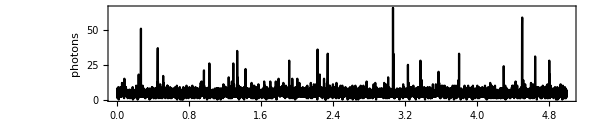

```mathematica
FMCStrace[{{1,1,0,0}},1.,0,5.,PlotStyle->Black]
```

route2 only:

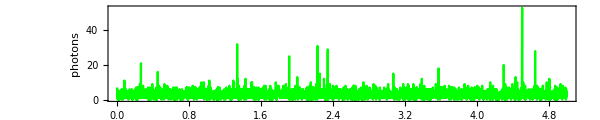

```mathematica
FMCStrace[{{0,1,0,0}},1.,0,5.,PlotStyle->Green]
```

data of route1:

```mathematica
FMCStrace[{{0,1,0,0}},1.,0,10.,FOutput->FData]
```

{{{0.,7.},{0.001,6.},{0.002,5.},{0.003,6.},{0.004,1.},{0.005,1.},{0.006,1.},{0.007,3.},{0.008,2.},{0.009,0.},9980,{9.99,1.},{9.991,2.},{9.992,2.},{9.993,3.},{9.994,1.},{9.995,1.},{9.996,4.},{9.997,3.},{9.998,2.},{9.999,3.}}}
 |  |  |  |

Whole measurement with one second binning

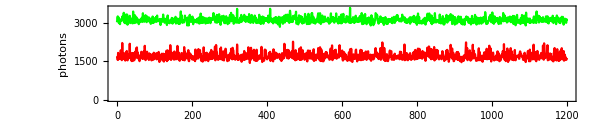

```mathematica
FMCStrace[{{1,0,0,0},{0,1,0,0}},1000.,0,5000.]
```

Indicate beginnings and endings of identified bursts:

```mathematica
FDetermineBackground[](*returns estimated background rates in counts per seconds*)
FFindBurstsDeltaT[0.00015,20,10000]
FDetermineBackground[](*returns estimated background rates in counts per seconds*)
FFindBurstsDeltaT[0.00015,50,10000]
```

{1716.39,3138.61,0.,0.,0.,0.}

6968

{1578.63,3044.98,0.,0.,0.,0.}

2344

```mathematica
FMCStrace[{{1,0,0,0},{0,1,0,0}},1,0,5,FShowBursts->True,FShowBurstsLevel->40,FBurstData->All]
```

-Graphics-

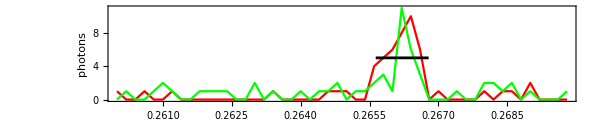

```mathematica
FMCStrace[{{1,0,0,0},{0,1,0,0}},0.2,0.26,0.27,FShowBursts->True,FShowBurstsLevel->5,FBurstData->All]
```

See the PIE section for an example of FMCStrace using channel constraints.

| Related Guides
▪Fretica